## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="FBA2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "fit_FBA2";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/test bla/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00019 | 0.00016
0.00022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00024 | 0.00021
0.00027 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00085 | 0.0008075
0.0008925 |  | M | 7.5 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 10.5 | 9.83
11.2 | 1/s | 8 | 30 | trishcl | 0.05 | 
1 | fdp | Null | 8.17 | 7.73
8.6 | 1/s | 8 | 30 | trishcl | 0.05 | 
1 | fdp | Null | 10.33 | 10.03
10.63 | 1/s | 8 | 30 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | dhap | 0.00013 | 0.000119
0.000141 |  | Competitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.00003 | 0.000025
0.000035 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.00023 | 0.000188
0.000272 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kic | dhap | 9.×10^-6 | 7.8×10^-6
0.0000102 |  | Competitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.000118 | 0.000095
0.000141 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.000221 | 0.000194
0.000248 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0,0,0};
s05Priorities = Null;
kcatPriorities = {1,0,0};
inhibitionPriorities={1,1,1,0,0,0};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 0.00016 | 0.000152
0.000168 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 10.5 | 9.83
11.2 | 1/s | 8 | 30 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | dhap | 0.00013 | 0.000119
0.000141 |  | Competitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.00003 | 0.000025
0.000035 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.00023 | 0.000188
0.000272 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
rxn
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

```mathematica
catalyticBranch={"E_FBA2[c] + fdp[c] <=> E_FBA2[c]&fdp",
				"E_FBA2[c]&fdp <=> E_FBA2[c]&dhap&g3p",
				"E_FBA2[c]&dhap&g3p <=> E_FBA2[c]&dhap + g3p[c]",
				"E_FBA2[c]&dhap <=> E_FBA2[c] + dhap[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((FBA2^c)_^+fdp^c⇌(FBA2^c&fdp^c)_^)^FBA21,((FBA2^c&dhap^c)_^⇌(FBA2^c)_^+dhap^c)^FBA22,((FBA2^c&fdp^c)_^⇌(FBA2^c&dhap^c&g3p^c)_^)^FBA23,((FBA2^c&dhap^c&g3p^c)_^⇌(FBA2^c&dhap^c)_^+g3p^c)^FBA24}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((FBA2^c)_^+fdp^c⇌(FBA2^c&fdp^c)_^)^FBA21,Overscript[(FBA2^c&dhap^c)_^⇌(FBA2^c)_^+dhap^c, FBA22],((FBA2^c&fdp^c)_^⇌(FBA2^c&dhap^c&g3p^c)_^)^FBA23,Overscript[(FBA2^c&dhap^c&g3p^c)_^⇌(FBA2^c&dhap^c)_^+g3p^c, FBA24]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Setup King-Altman Equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={{"prod_inhib_dhap",m["g3p","c"]->10^-10},{"prod_inhib_g3p",m["dhap","c"]->10^-10}};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

## Semi-Automated Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0144975}

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	fdp[c]	g3p[c]	param_FBA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/haldaneRatio_1.txt"	0.00016
1	0	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt"	0.09090909090909094
1	0	0.00002694318427183895	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt"	0.1368068886032101
1	0	0.000042702069335662915	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt"	0.20076000891310194
1	0	0.0000676782189940945	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt"	0.28474724895080133
1	0	0.00010726274856163285	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt"	0.386863179846857
1	0	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.0002694318427183895	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0004270206933566291	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt"	0.7152527510491988
1	0	0.0006767821899409458	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt"	0.7992399910868985
1	0	0.0010726274856163284	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt"	0.9090909090909091
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt"	10.5
1	0.000065	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.06250000000000003
1	0.000065	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.17411239489546837
1	0.000065	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.4000000000000001
1	0.000065	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.6782688399674106
1	0.000065	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.8695652173913043
1	0.00013	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.04761904761904764
1	0.00013	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.13652705949581437
1	0.00013	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.3333333333333335
1	0.00013	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.6125741132772069
1	0.00013	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.8333333333333333
1	0.00026	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.032258064516129045
1	0.00026	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.09535767393826002
1	0.00026	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.2500000000000001
1	0.00026	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.5131670194948621
1	0.00026	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt"	0.7692307692307693
1	0	0.000017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.030349681108423142
1	0	0.00005375872022286247	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.08852308825306443
1	0	0.00017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.22475570032573297
1	0	0.0005375872022286248	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.43782901894103
1	0	0.0017000000000000008	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.6252831898504759
1	0	0.000017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.01821541710665259
1	0	0.00005375872022286247	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.05425730412803112
1	0	0.00017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.14495798319327732
1	0	0.0005375872022286248	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.3075252527148365
1	0	0.0017000000000000008	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.4765193370165746
1	0	0.000017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.010121754437435824
1	0	0.00005375872022286247	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.030581863846891433
1	0	0.00017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.08476658476658477
1	0	0.0005375872022286248	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.1927783983056278
1	0	0.0017000000000000008	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_g3p.txt"	0.32288254562470753

### Sanity check plots

```mathematica
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
assumedSaturatingConc=0.01;
eTotal=1;
logStepSize=0.5;
inhibFittingData=simulateInhibData[rxn, metsFull, metSatForSub, metSatRevSub,  inhibitionList,  assumedSaturatingConc, eTotal,
			   logStepSize, activeIsoSub, bufferInfo, ionCharge, inputPath, fileList];
```

#### C inhib of dhap by glyc3p

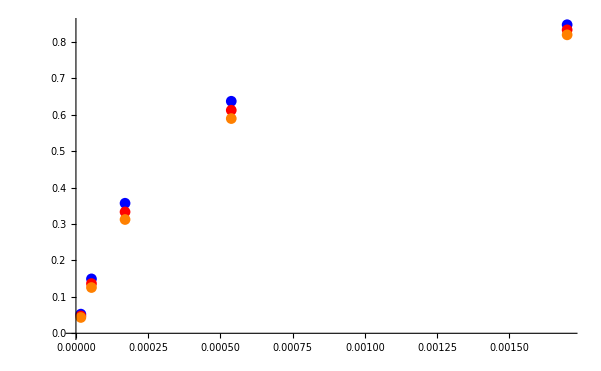

```mathematica
inhib1=inhibFittingData[[1;;5,{3,-1}]];
inhib2=inhibFittingData[[6;;10,{3,-1}]];
inhib3=inhibFittingData[[11;;15,{3,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.,0.000255}

{1.,0.00034}

{1.,0.00051}

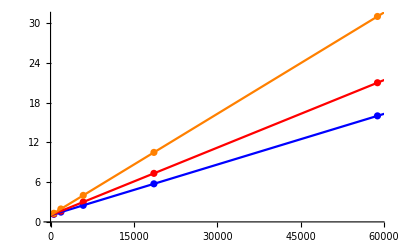

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,0,100000}, PlotStyle->{Blue,Red, Orange}]]
```

```mathematica
0.000065/((0.000255/0.00017)-1)
```

0.00013

```mathematica
0.00013/((0.00033999999999999997/0.00017)-1)
```

0.00013

```mathematica
0.00026/((0.0005099999999999999/0.00017)-1)
```

0.00013

#### NC inhib of nadph by glyc3p

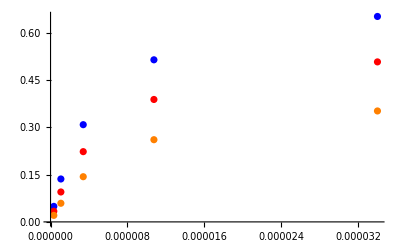

```mathematica
inhib1=inhibFittingData[[16;;20,{4,-1}]];
inhib2=inhibFittingData[[21;;25,{4,-1}]];
inhib3=inhibFittingData[[26;;30,{4,-1}]];
ListPlot[{inhib1, inhib2, inhib3}, PlotStyle->{Blue,Red, Orange}]
```

{1.34615,6.46×10^-6}

{1.69231,9.52×10^-6}

{2.38462,0.00001564}

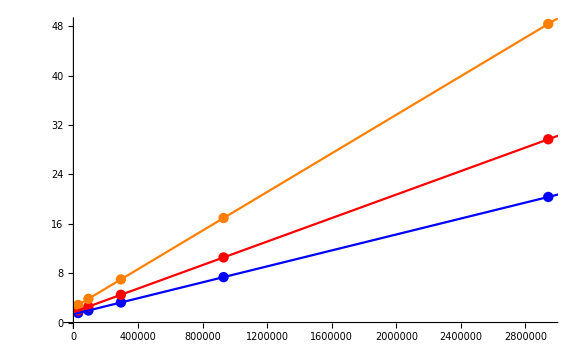

```mathematica
lm1=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib1],x,x];
lm2=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib2],x,x];
lm3=LinearModelFit[Map[{1/#[[1]],1/#[[2]]}&,inhib3],x,x];
lm1["ParameterTableEntries"][[All,1]]
lm2["ParameterTableEntries"][[All,1]]
lm3["ParameterTableEntries"][[All,1]]
Show[ListPlot[{Map[{1/#[[1]],1/#[[2]]}&,inhib1], Map[{1/#[[1]],1/#[[2]]}&,inhib2],
Map[{1/#[[1]],1/#[[2]]}&,inhib3]}, PlotStyle->{Blue,Red, Orange}],
Plot[{lm1[x],lm2[x],lm3[x]},{x,-100,10^7}, PlotStyle->{Blue,Red, Orange}]]
```

```mathematica
Vmapp = -1/1.346153846153847
```

-0.742857

```mathematica
0.000065/((1/0.7428571428571424)-1)
```

0.000187778

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«18 more identical outputs»

```mathematica
FilePrint[dataPathList[[18]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=100;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	20
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[/home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateFor.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/absRateRev.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateFor_fdp.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateRev_dhap.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/relRateRev_g3p.txt, /home/mrama/Dropbox/test bla/MASSef/examples/fit_FBA2/input/prod_inhib_dhap.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	16
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateRev_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: nan
best_fit: 16.8802860779
best_fit: 9.20538280096
best_fit: nan
best_fit: 45.282506772
best_fit: 42.5130547847
best_fit: 15.0416971013
best_fit: 1.09998659934
best_fit: 1.05740807443
best_fit: 69.0509284422
best_fit: 0.942509123982
best_fit: 59.6105653692
best_fit: 499.434742455
best_fit: 119.566498769
best_fit: 0.875269059129
best_fit: 726.93359987
best_fit: 59.3367901663
best_fit: 23.7320159461
best_fit: 24.2212054868
best_fit: 1.0062220457
best_fit: 58.0929092129
best_fit: 27.8556856612
best_fit: 0.941725435783
best_fit: nan
best_fit: 268.563508224
best_fit: 49.9828782613
best_fit: 66.7707362385
best_fit: 11.1953178809
best_fit: 9.84079608293
best_fit: 165.987814888
best_fit: nan
best_fit: 27.8870192161
best_fit: 152.217039816
best_fit: 199.792267669
best_fit: nan
best_fit: 21.1424500858
best_fit: 330.734552554
best_fit: 78.7895293363
best_fit: 215.553953966
best_fit: 309.935325108
best_fit: nan
best_fit: 91.5586245827
best_fit: nan
best_fit: 96.2570748465
best_fit: nan
best_fit: 1.05994652599
best_fit: 25.7935884092
best_fit: nan
best_fit: 86.0220043513
best_fit: 32.8346548748
best_fit: 44.6716755121
best_fit: 39.0432273535
best_fit: 4.61238044529
best_fit: 177.49465736
best_fit: 0.683251836821
best_fit: 112.457762021
best_fit: 44.0880961091
best_fit: 23.015067458
best_fit: 33.1404578708
best_fit: 28.4837860633
best_fit: 125.853039836
best_fit: 316.702694682
best_fit: 0.827259733153
best_fit: nan
best_fit: 0.974138032897
best_fit: nan
best_fit: 171.515684715
best_fit: 13.85281137
best_fit: 186.664673581
best_fit: 46.6804095065
best_fit: 2.6390250416
best_fit: 53.5683628127
best_fit: 136.528317843
best_fit: 42.0795339953
best_fit: 36.1080402414
best_fit: 65.9282036191
best_fit: 70.8086245054
best_fit: 144.374084661
best_fit: nan
best_fit: 1.07906078193
best_fit: 58.5183814513
best_fit: 47.7860467598
best_fit: 0.964116748537
best_fit: 289.544923444
best_fit: 39.6830087434
best_fit: 121.485699299
best_fit: 216.280492091
best_fit: 1.01959936616
best_fit: 567.869442692
best_fit: nan
best_fit: 36.8767541953
best_fit: 62.3646977353
best_fit: 2.7971729317
best_fit: 173.40065944
best_fit: 100.15812826
best_fit: 108.095128211
best_fit: nan
best_fit: 0.991657962172
best_fit: nan
best_fit: nan

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.000566341 | 3.20742×10^-7 | 2.08784×10^-7 | 0.13049 | 0.00016 | 0.000160209
1 | haldaneRatio_1 | 0.000566341 | 3.20742×10^-7 | 2.08784×10^-7 | 0.13049 | 0.00016 | 0.000160209
1 | haldaneRatio_1 | 0.000566341 | 3.20742×10^-7 | 2.08784×10^-7 | 0.13049 | 0.00016 | 0.000160209
1 | haldaneRatio_1 | 0.000566341 | 3.20742×10^-7 | 2.08784×10^-7 | 0.13049 | 0.00016 | 0.000160209
1 | haldaneRatio_1 | 0.000566341 | 3.20742×10^-7 | 2.08784×10^-7 | 0.13049 | 0.00016 | 0.000160209
1 | haldaneRatio_1 | 0.000566341 | 3.20742×10^-7 | 2.08784×10^-7 | 0.13049 | 0.00016 | 0.000160209
1 | haldaneRatio_1 | 0.000566341 | 3.20742×10^-7 | 2.08784×10^-7 | 0.13049 | 0.00016 | 0.000160209
1 | haldaneRatio_1 | 0.000566341 | 3.20742×10^-7 | 2.08784×10^-7 | 0.13049 | 0.00016 | 0.000160209
1 | haldaneRatio_1 | 0.000566341 | 3.20742×10^-7 | 2.08784×10^-7 | 0.13049 | 0.00016 | 0.000160209
1 | haldaneRatio_1 | 0.000566341 | 3.20742×10^-7 | 2.08784×10^-7 | 0.13049 | 0.00016 | 0.000160209
1 | haldaneRatio_1 | 0.000566341 | 3.20742×10^-7 | 2.08784×10^-7 | 0.13049 | 0.00016 | 0.000160209
1 | relRateFor_fdp | 1.47029×10^-6 | 2.16175×10^-12 | 3.07769×10^-7 | 0.000338546 | 0.0909091 | 0.0909088
1 | relRateFor_fdp | 1.26729×10^-6 | 1.60601×10^-12 | 3.99207×10^-7 | 0.000291803 | 0.136807 | 0.136806
1 | relRateFor_fdp | 9.84426×10^-7 | 9.69094×10^-13 | 4.55067×10^-7 | 0.000226672 | 0.20076 | 0.20076
1 | relRateFor_fdp | 6.12954×10^-7 | 3.75713×10^-13 | 4.01886×10^-7 | 0.000141138 | 0.284747 | 0.284747
1 | relRateFor_fdp | 1.61298×10^-7 | 2.60171×10^-14 | 1.43682×10^-7 | 0.0000371402 | 0.386863 | 0.386863
1 | relRateFor_fdp | 3.39109×10^-7 | 1.14995×10^-13 | 3.90414×10^-7 | 0.0000780827 | 0.5 | 0.5
1 | relRateFor_fdp | 8.39526×10^-7 | 7.04804×10^-13 | 1.18524×10^-6 | 0.000193308 | 0.613137 | 0.613138
1 | relRateFor_fdp | 1.29121×10^-6 | 1.66723×10^-12 | 2.12654×10^-6 | 0.000297314 | 0.715253 | 0.715255
1 | relRateFor_fdp | 1.66275×10^-6 | 2.76473×10^-12 | 3.05999×10^-6 | 0.000382862 | 0.79924 | 0.799243
1 | relRateFor_fdp | 1.94571×10^-6 | 3.78578×10^-12 | 3.86725×10^-6 | 0.000448017 | 0.863193 | 0.863197
1 | relRateFor_fdp | 2.14887×10^-6 | 4.61765×10^-12 | 4.49816×10^-6 | 0.000494798 | 0.909091 | 0.909095
1 | absRateFor | 4.21693×10^-10 | 1.77825×10^-19 | 1.01953×10^-8 | 9.70985×10^-8 | 10.5 | 10.5
1 | absRateFor | 4.21693×10^-10 | 1.77825×10^-19 | 1.01953×10^-8 | 9.70985×10^-8 | 10.5 | 10.5
1 | absRateFor | 4.21693×10^-10 | 1.77825×10^-19 | 1.01953×10^-8 | 9.70985×10^-8 | 10.5 | 10.5
1 | absRateFor | 4.21693×10^-10 | 1.77825×10^-19 | 1.01953×10^-8 | 9.70985×10^-8 | 10.5 | 10.5
1 | absRateFor | 4.21693×10^-10 | 1.77825×10^-19 | 1.01953×10^-8 | 9.70985×10^-8 | 10.5 | 10.5
1 | absRateFor | 4.21693×10^-10 | 1.77825×10^-19 | 1.01953×10^-8 | 9.70985×10^-8 | 10.5 | 10.5
1 | absRateFor | 4.21693×10^-10 | 1.77825×10^-19 | 1.01953×10^-8 | 9.70985×10^-8 | 10.5 | 10.5
1 | absRateFor | 4.21693×10^-10 | 1.77825×10^-19 | 1.01953×10^-8 | 9.70985×10^-8 | 10.5 | 10.5
1 | absRateFor | 4.21693×10^-10 | 1.77825×10^-19 | 1.01953×10^-8 | 9.70985×10^-8 | 10.5 | 10.5
1 | absRateFor | 4.21693×10^-10 | 1.77825×10^-19 | 1.01953×10^-8 | 9.70985×10^-8 | 10.5 | 10.5
1 | absRateFor | 4.21693×10^-10 | 1.77825×10^-19 | 1.01953×10^-8 | 9.70985×10^-8 | 10.5 | 10.5
1 | prod_inhib_dhap | 2.15103×10^-6 | 4.62695×10^-12 | 3.09558×10^-7 | 0.000495293 | 0.0625 | 0.0624997
1 | prod_inhib_dhap | 1.3738×10^-6 | 1.88732×10^-12 | 5.50767×10^-7 | 0.000316328 | 0.174112 | 0.174112
1 | prod_inhib_dhap | 9.24927×10^-7 | 8.5549×10^-13 | 8.51888×10^-7 | 0.000212972 | 0.4 | 0.399999
1 | prod_inhib_dhap | 5.62526×10^-7 | 3.16435×10^-13 | 8.78536×10^-7 | 0.000129526 | 0.678269 | 0.678268
1 | prod_inhib_dhap | 3.37593×10^-7 | 1.13969×10^-13 | 6.75944×10^-7 | 0.0000777336 | 0.869565 | 0.869565
1 | prod_inhib_dhap | 1.68995×10^-6 | 2.85592×10^-12 | 1.85297×10^-7 | 0.000389124 | 0.047619 | 0.0476189
1 | prod_inhib_dhap | 4.12993×10^-7 | 1.70563×10^-13 | 1.29831×10^-7 | 0.0000950951 | 0.136527 | 0.136527
1 | prod_inhib_dhap | 8.44436×10^-8 | 7.13071×10^-15 | 6.48128×10^-8 | 0.0000194438 | 0.333333 | 0.333333
1 | prod_inhib_dhap | 7.73082×10^-8 | 5.97656×10^-15 | 1.09044×10^-7 | 0.0000178009 | 0.612574 | 0.612574
1 | prod_inhib_dhap | 1.33892×10^-7 | 1.79271×10^-14 | 2.56915×10^-7 | 0.0000308298 | 0.833333 | 0.833333
1 | prod_inhib_dhap | 2.1457×10^-6 | 4.60401×10^-12 | 1.59375×10^-7 | 0.000494063 | 0.0322581 | 0.0322579
1 | prod_inhib_dhap | 3.64017×10^-7 | 1.32508×10^-13 | 7.99269×10^-8 | 0.000083818 | 0.0953577 | 0.0953578
1 | prod_inhib_dhap | 8.93956×10^-7 | 7.99158×10^-13 | 5.14603×10^-7 | 0.000205841 | 0.25 | 0.250001
1 | prod_inhib_dhap | 6.42086×10^-7 | 4.12275×10^-13 | 7.58697×10^-7 | 0.000147846 | 0.513167 | 0.513168
1 | prod_inhib_dhap | 2.24279×10^-7 | 5.03013×10^-14 | 3.97248×10^-7 | 0.0000516423 | 0.769231 | 0.769231
1 | prod_inhib_g3p | 0.000129601 | 1.67965×10^-8 | 9.05823×10^-6 | 0.0298462 | 0.0303497 | 0.0303587
1 | prod_inhib_g3p | 0.0000997601 | 9.95207×10^-9 | 0.0000203366 | 0.0229732 | 0.0885231 | 0.0885434
1 | prod_inhib_g3p | 0.0000325575 | 1.05999×10^-9 | 0.0000168498 | 0.00749693 | 0.224756 | 0.224773
1 | prod_inhib_g3p | 0.0000481382 | 2.31728×10^-9 | 0.0000485273 | 0.0110836 | 0.437829 | 0.43778
1 | prod_inhib_g3p | 8.08301×10^-6 | 6.5335×10^-11 | 0.0000116375 | 0.00186116 | 0.625283 | 0.625272
1 | prod_inhib_g3p | 0.000182987 | 3.34844×10^-8 | 7.67658×10^-6 | 0.0421433 | 0.0182154 | 0.0182231
1 | prod_inhib_g3p | 0.000149327 | 2.22984×10^-8 | 0.0000186589 | 0.0343896 | 0.0542573 | 0.054276
1 | prod_inhib_g3p | 0.0000669 | 4.47561×10^-9 | 0.0000223315 | 0.0154055 | 0.144958 | 0.14498
1 | prod_inhib_g3p | 0.0000467887 | 2.18918×10^-9 | 0.0000331294 | 0.0107729 | 0.307525 | 0.307492
1 | prod_inhib_g3p | 4.2297×10^-6 | 1.78904×10^-11 | 4.64096×10^-6 | 0.00097393 | 0.476519 | 0.476524
1 | prod_inhib_g3p | 0.000263333 | 6.9344×10^-8 | 6.13914×10^-6 | 0.0606529 | 0.0101218 | 0.0101279
1 | prod_inhib_g3p | 0.000228366 | 5.21512×10^-8 | 0.0000160852 | 0.0525971 | 0.0305819 | 0.0305979
1 | prod_inhib_g3p | 0.000135683 | 1.84098×10^-8 | 0.000026487 | 0.031247 | 0.0847666 | 0.0847931
1 | prod_inhib_g3p | 7.00834×10^-6 | 4.91168×10^-11 | 3.1109×10^-6 | 0.00161372 | 0.192778 | 0.192775
1 | prod_inhib_g3p | 0.0000502743 | 2.5275×10^-9 | 0.0000373793 | 0.0115767 | 0.322883 | 0.32292

### Simulated Data and Best Fit Data Plot

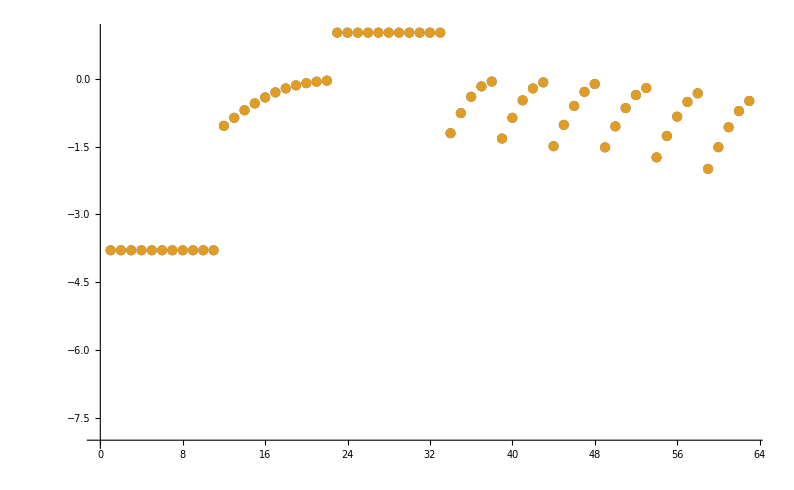

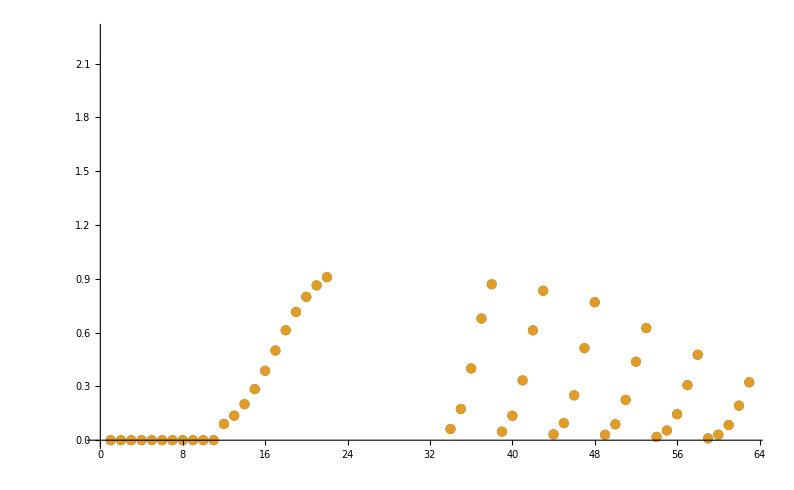

```mathematica
datasetI=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.00017 | 0.000170091 | 0.0533789

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
10.5 | 10.5 | 0.0000679152

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00016 | 0.000166408 | 4.00487